∫_a^b √(1+df[x]^2)ⅆx

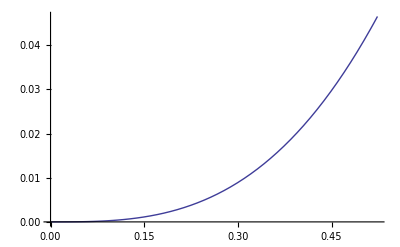

0.52725

```mathematica
(* Name: Jenny Chen *)
(* MATH2262B: Analytic Geometry and Calculus II *)
(* Mathematica Project 1 *)

(* 1. Solve problems 11-16 on page 388 *)

(* Example *)
(* y = Sin[x]-x*Cos[x], 0≤x≤Pi/6 *)
a=0;
b=Pi/6;
f[x_]:=Sin[x]-x*Cos[x];
df[x_]:=f'[x];
(* a. Set up an integral for the length of the curve. *)
Defer[Integrate[Sqrt[1+(df[x])^2],{x,a,b}]]
(* b. Graph the curve to see what it looks like. *)
Plot[f[x],{x,a,b}]
(* c. Use your grapher's or computer's integral evaluator to find the curve's length numerically. *)
 L=NIntegrate[Sqrt[1+(df[x])^2],{x,a,b}]
```

∫_a^b 2 π f[x] √(1+df[x]^2)ⅆx

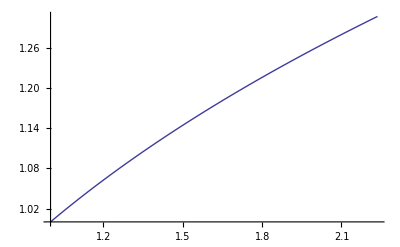

-Graphics3D-

-Graphics3D-

-Graphics3D-

9.343

```mathematica
(* 2. Do the same as in (1.) for the problems 37-42 on page 389 *)

(* 3. Solve problems 1,2,4,6 on page 393 *)

(* Example *)
(* y = x^(1/3), 1≤x≤Sqrt[5], x-axis*)
a= 1;
b= Sqrt[5];
f[x_]:= x^(1/3);
df[x_]:=f'[x];
(* a. Set up an integral for the area of the surface generated by revolving the givem curve about the indicated axis *)
Defer[Integrate[2Pi*f[x]*Sqrt[1+(df[x])^2],{x,a,b}]]
(* b. Graph the curve to see what it looks like. If you can, graph the surface too (Choose the correct one!).*)
Plot[f[x],{x,a,b}]
RevolutionPlot3D[f[x],{x,a,b},RevolutionAxis->"x"]
RevolutionPlot3D[f[x],{x,a,b},RevolutionAxis->"y"]
RevolutionPlot3D[f[x],{x,a,b},RevolutionAxis->"z"]
(* c. Use your grapher's or computer's integral evaluator to find the surface's area numerically. *)
A=NIntegrate[2Pi*f[x]*Sqrt[1+(df[x])^2],{x,a,b}]
```